# Documentazione: chess tactics for beginners

## Wolfram Knights

## Progetto di Matematica Computazionale per l' anno accademico 2022/2023. Collaborators : Andrea Accornero, Andrea Bianchi, Mattia Frega, Gabriele Magazzù .

## Scopo del package

Chess tactics for beginners è un package Wolfram Mathematica che nasce con l’obiettivo di rendere usufruibile e interattivo l’apprendimento del gioco degli scacchi, per chiunque, attraverso Wolfram Mathematica. 
L’idea è che l’utente si eserciti per essere in grado di chiudere la partita di fronte ad uno scacco matto in una mossa.

Il package prevede tre fasi:

fase generazione ...

fase verifica....

ultima fase non ricordo quale....

## Istruzioni

All’avvio, il programma chiede all’utente il proprio nome poi mostra la scacchiera e i comandi di gioco.

-Graphics-

Pulsanti funzionali / di gioco:

Nuova Scacchiera: permette di generare una nuova partita con scacco matto in una mossa.

Restart: dopo aver giocato, permette di resettare la scacchiera.

Verifica Mossa: dopo aver giocato, permette di verificare se la mossa effettuata è quella corretta.

Rigioca Partita: se si ha sbagliato a giocare o vogliamo rigiocare nuovamente la partita, premendo questo tasto si può ricaricare l’ultima scacchiera.

Pulsanti per la personalizzazione:

Dimensione Scacchiera: permette di switchare la dimensione della scacchiera tra le 4 dimensioni pre-disponibili.

-Graphics- : icona del ColorSetter per poter scegliere un colore RGB da applicare alla scacchiera.

Colora Scacchiera: permette di cambiare il colore della scacchiera a quello scelto tramite il ColorSetter.

Reset Colore: riporta il colore allo stato iniziale, di default, ovvero RGBColor[0.8196,0.5451,0.2784];

## Il dataset delle partite

Il dataset delle partite che abbiamo usato è un file contenente, per ogni partita, una stringa PGN e alcuni metadati. Il file viene parsato al caricamento del package e il caricamento di una nuova scacchiera corrisponde all’estrazione casuale di una partita dal dataset.

## La fase di gioco

```mathematica
Move[move1]
```

The situation after the move is displayed by Chess[]:

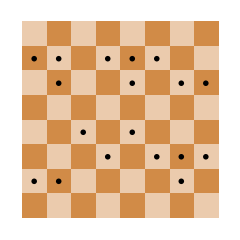

```mathematica
Chess[]
```

Next move could also be randomly found, this time black is to move:

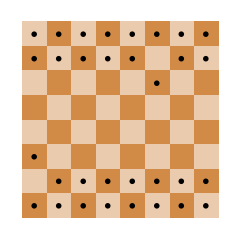

```mathematica
Move[RandomMove];Chess[]
```

## Approfondimento package Chess-Master

## Scelte progettuali

## Note e lavori futuri

Pieces includes all pieces, including the virtual pieces piece0 and piece33:

```mathematica
{piece0,piece33}
```

{<|id→0,image→{},status→enpassant,pos→{{}}|>,<|id→33,image→{},status→enpassant,pos→{{}}|>}

The properties of each piece is embedded in the association piece#, where # is the piece number.

The image of each piece is downloaded or kept in the mx-file pieceImages.mx:

```mathematica
GraphicsGrid[Partition[#[image]&/@Most@Rest@Pieces,16],ImageSize->500]
```

Standard positions are obtained by executing Startposition:

```mathematica
Startposition
```

whiteoptionlist and blackoptionlist display move options of all pieces by x- and y-coordinates:

```mathematica
whiteoptionlist
```

<|1→{{1,3},{1,4}},2→{{2,3},{2,4}},3→{{3,3},{3,4}},4→{{4,3},{4,4}},5→{{5,3},{5,4}},6→{{6,3},{6,4}},7→{{7,3},{7,4}},8→{{8,3},{8,4}},9→{{1,3},{3,3}},10→{{6,3},{8,3}}|>

```mathematica
blackoptionlist
```

<|17→{{1,6},{1,5}},18→{{2,6},{2,5}},19→{{3,6},{3,5}},20→{{4,6},{4,5}},21→{{5,6},{5,5}},22→{{6,6},{6,5}},23→{{7,6},{7,5}},24→{{8,6},{8,5}},25→{{1,6},{3,6}},26→{{6,6},{8,6}}|>

A move may be selected randomly by RandomMove:

```mathematica
move1=RandomMove
```

{1,{1,3}}

The status of this piece number is

```mathematica
#[status]&/@Select[Pieces,#[id]===move1[[1]]&]
```

{pawn}

and the move is to

```mathematica
Coord[move1[[2]]]
```

a3

The function Move is used to move the piece:

```mathematica
Move[move1]
```

The situation after the move is displayed by Chess[]:

```mathematica
Chess[]
```

-Graphics-

Next move could also be randomly found, this time black is to move:

```mathematica
Move[RandomMove];Chess[]
```

-Graphics-

And so on ...

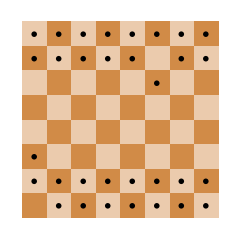

```mathematica
Move[RandomMove];Chess[]
```